# Метод на допирателните (Нютон)

Дадено е уравнението:
x^2 - 33sin(x + π/(p + 1)) - (p + 2q)= 0, където p и q са съответно предпоследната и последната цифра от факултетния ни номер.
x^2 - 33sin(x + π/2) - 19 = 0
1. Да се намери общия брой на корените на уравнението.
2. Да се локализира най-малкия реален корен в интервал [a, b].
3. Да се проверят условията за приложение на метода на допирателните (Нютон).
4. Да се определи началното приближение за итерационния процес по метода на допирателните (Нютон).
5. Да се изчисли корена по метода на допирателните с точност 0,0000000001. Представете таблица с изчисленията.
6. Да се провери колко итерации биха били необходими, ако се използва метода на разполовяването в същия интервал [a, b] за същата точност.
7. Да се направи сравнение кой метод е по-ефективен за избрания интервал.

```mathematica
f[x_] := x^2 - 33Sin[x + π/2] - 19
```

```mathematica
f[x]
```

-19+x^2-33 Cos[x]

## 1. Да се намери общия брой на корените на уравнението.

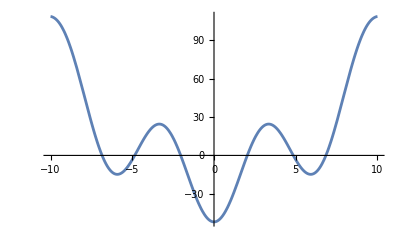

```mathematica
Plot[f[x], {x, -10, 10}]
```

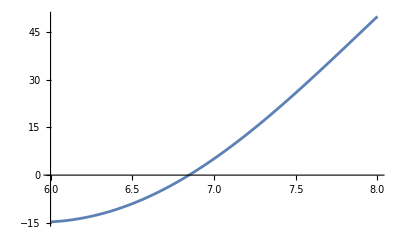

```mathematica
Plot[f[x], {x, 6, 8}]
```

Брой корени: 6

## 2. Да се локализира най-малкия реален корен в интервал [a, b].

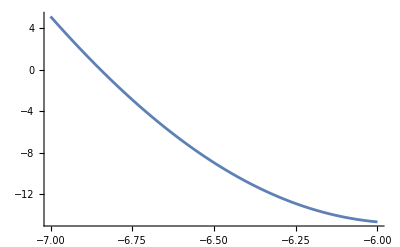

```mathematica
Plot[f[x], {x, -7, -6}]
```

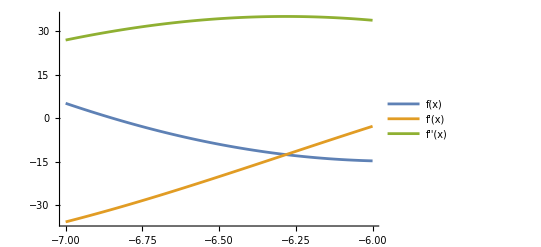

```mathematica
Plot[{f[x], f'[x], f''[x]}, {x, -7, -6}, PlotLegends->"Expressions"]
```

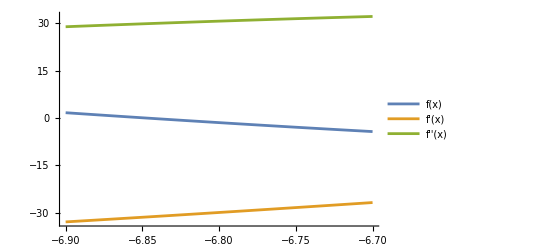

```mathematica
Plot[{f[x], f'[x], f''[x]}, {x, -6.9, -6.7}, PlotLegends->"Expressions"]
```

```mathematica
f[-6.9]
```

1.69107

```mathematica
f[-6.7]
```

-4.28464

Извод:
1. f(-6.9) = 1.691.. > 0
2. f(-6.7) = -4.284... < 0
Следователно в двата края на функцията има различни знаци и функцията е непрекъсната в избрания интервал [-6.9;-6.7]. Следва, че функцията има поне един корен в дадения интервал.

## 3. Проверка на условията за сходимост

### Проверка на първата производна

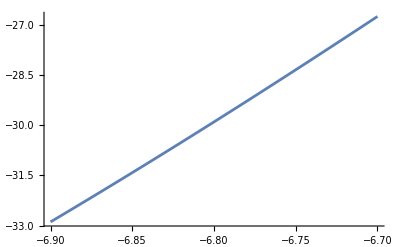

```mathematica
Plot[f'[x], {x, -6.9, -6.7}]
```

Извод: (1) Стойностите на първата производна в разглеждания интервал [-6.9; -6.7] са между -33 и -27. Следователно първата f’(x) < 0 в целия разглеждан интервал [-6.9; -6.7].

### Проверка на втората производна

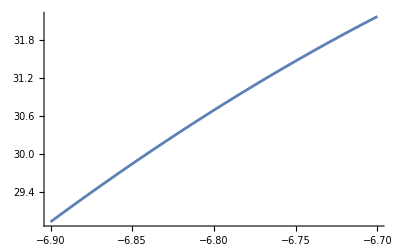

```mathematica
Plot[f''[x], {x, -6.9, -6.7}]
```

Извод: (2) Стойностите на първата производна в разглеждания интервал [-6.9; -6.7] са между 28 и 33. Следователно втората f''(x) > 0 в целия разглеждан интервал [-6.9; -6.7].

Извод: от (1) и (2) следва, че f'(x) и f''(x) са с постоянни знаци в разглеждания интервал [-6.9; -6.7] => Методът на допирателните е сходящ.

## 4. Избор на начално приближение

f’’ > 0 за текущата задача. Следователно избираме x0 , така че f(x_0).f’’ > 0.
=> f(x_0) > 0
=> x_0 = -6.9

### Пресмятане на постоянните величини:

```mathematica
Plot[Abs[f''[x]], {x, -6.9, -6.7}]
```

-Graphics-

От геометрични съображения максимума се достига в десния край на интервала, а минимума - в левия.

```mathematica
М2 = Abs[f''[-6.9]]
```

28.9189

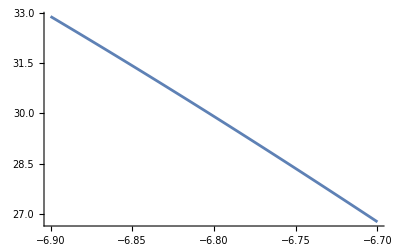

```mathematica
Plot[Abs[f'[x]], {x, -6.9, -6.7}]
```

От геометрични съображения максимума се достига в левия край на интервала, а минимума - в десния.

```mathematica
m1 = Abs[f'[-6.7]]
```

26.76

```mathematica
p = М2/(2m1)
```

0.540338

## 5.Да се изчисли корена по метода на допирателните с точност 0,0000000001

```mathematica
f[x_]:=   x^2 - 33Sin[x + π/2] - 19
x0 = -6.9;
М2 = Abs[f''[-6.9]];
m1 = Abs[f'[-6.7]];
p = М2/(2m1);
epszad = 0.0000000001;
eps = 1;
Print["n = ",0,  " x_n = ", x0, " f(x) = ", f[x0], " f'(x) = ", f'[x0]];
For[n = 1, eps > epszad, n++,
x1 = x0 - f[x0]/f'[x0];
Print["n = ",n,  " x_n = ", x1, " f(x_n) = ", f[x1] " f'(x_n) = ", f'[x1], " ε_n = ", eps = p* (x1 - x0)^2];
x0 = x1
]
```

n = 0 x_n = -6.9 f(x) = 1.69107 f'(x) = -32.8885

n = 1 x_n = -6.84858 f(x_n) = 0.0386531  f'(x_n) = -31.3769 ε_n = 0.00142857

n = 2 x_n = -6.84735 f(x_n) = 0.0000226662  f'(x_n) = -31.3401 ε_n = 8.2×10^-7

n = 3 x_n = -6.84735 f(x_n) = 7.81597×10^-12  f'(x_n) = -31.3401 ε_n = 2.82631×10^-13

## 6. Да се провери колко итерации биха били необходими, ако се използва метода на разполовяването в същия интервал [a, b] за същата точност

```mathematica
Log2[(-6.7 + 6.9)/0.0000000001] - 1
```

29.8974

## 6. Да се направи сравнение кой метод е по-ефективен за избрания интервал

Извод: По метода на допирателните (Нютон) биха били необходими 4 итерации за достигане на исканата точност. А по метода на разполовяването са необходими 30 итерации. Следователно методът на допирателните е по-ефективен за избрания интервал [-6.9, -6.7].